# Inlämningsuppgift 1: Problemlösning

IX1307 Problemlösning i Matematik, Inlämningsuppgift 1a, HT2019

Av Samuel Ferrara

## 1. Inledning

## 3. Bakgrund

## 3. Problem

## 3.1 Polynomekvation

Hitta lösningarna till polynomekvationen: 2/3 x^5-2/3 x^4-8 x^3+8 x^2+18x-18=0. 
Rita också grafen för polynomet och markera nollställen med en röd punkt.

#### 3.1.1 Problemformulering

Uppgiften går ut på att lösa en polynomekvation av femte graden, och visiualisera lösningen genom att markera funktionens eventuella nollställen med röda punkter i dess graf. Vad som söks är de punkter på då funktionens graf  skär x-axeln, med andra ord då y=0. Ett polynom av femte graden har maximalt fem reella lösningar, vilket innebär att dess graf inte kan skära x-axeln på max fem olika ställen.

#### 3.1.2 Metod&Resultat

Det presenterade problemet löses enligt följande:

(1) Det första steget i lösningen är att en funktion för en godtycklig variabel x defineras.

```mathematica
f[x_]=2/3 x^5-2/3 x^4-8  x^3+8x^2+18x-18
```

-18+18 x+8 x^2-8 x^3-(2 x^4)/3+(2 x^5)/3

(2) Därefter beräknas funktionens  nollställen med hjälp av  kommandot “Solve”, där det anges att x1, x2, x3, x4 och x5 är element i x.

```mathematica
{x1,x2,x3,x4,x5}=x/.Solve[f[x]==0]
```

{-3,1,3,-√3,√3}

(3) Resultatet visualiseras genom att funktionens graf ritas upp med hjälp av funktionen “Plot”, xy-koordinaterna grafens skärningspunkter med y-axeln visualiseras även för att förtydliga sambandet mellan de röda prickarna och polynomekvationens beräknade resultat.

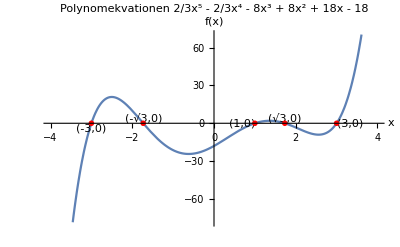

```mathematica
Plot[f[x],{x,-4,4},AxesLabel-> {"x","f(x)"}, PlotLabel -> "Polynomekvationen 2/3x^5 - 2/3x^4 - 8x^3 + 8x^2 + 18x - 18", Epilog -> {Text ["(-3,0)",{x1,f[x1]},Top],Text ["(1,0)",{x2,f[x2]},Right],Text ["(3,0)",{x3,f[x3]},Left],Text ["(-√3,0)",{x4,f[x4]},Bottom],Text ["(√3,0)",{x5,f[x5]},Bottom],
PointSize[0.01],Red,Point[{{x1,f[x1]},{x2,f[x2]},{x3,f[x3]},{x4,f[x4]},{x5,f[x5]}}]}]
```

#### 3.1.3 Diskussion

### 3.2 Ekvation med absolutbelopp

Lös ekvationen  |x-1|+|x-3|=4. Illustrera lösningsområdet grafiskt.

#### 3.2.1 Problemformulering